# Neural Network Explorations

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-4,4}]
```

```mathematica
Histogram[RandomVariate[NormalDistribution[0,1],40000],50]
```

```mathematica
sample[center_,num_]:=RandomVariate[MultinormalDistribution[center,IdentityMatrix[2]],num]
```

```mathematica
sample[{1,1},3]
```

```mathematica
clusters={sample[{-2,-2},10000],sample[{-2,2},10000],sample[{2,2},10000],sample[{2,-2},10000]};
```

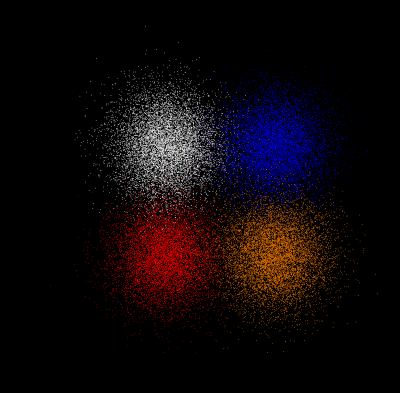

```mathematica
Graphics[{
AbsolutePointSize[0.5],
MapThread[{#1,Point[#2]}&,{{Red,White,Blue,Orange},clusters}]
},
Background->Black,
PlotRange->10,
Axes->True]
```

```mathematica
net=NetChain[{400,Ramp,4,SoftmaxLayer[]},"Input"->{2},"Output"->NetDecoder[{"Class",{Red,White,Blue,Orange}}]]
```

```mathematica
NetGraph[net]
```

```mathematica
net=NetInitialize[net]
```

```mathematica
data=RandomSample[
Join@@MapThread[
Thread[#1->#2]&,
{clusters,{Red,White,Blue,Orange}}]];
```

```mathematica
Take[data,20]//Column
```

```mathematica
Length[data]
```

```mathematica
training=Take[data,38000];
validation=Take[data,-2000];
```

```mathematica
result=NetTrain[net,training,MaxTrainingRounds->10000,ValidationSet->validation]
```

```mathematica
result[{0,0}]
```

```mathematica
result[{10,10}]
```

```mathematica
cm=ClassifierMeasurements[result,validation]
```

```mathematica
cm["Accuracy"]
```

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
With[{e=1},e]
```

```mathematica
With[{e=1},e]
```

```mathematica
With[{e=1},e]
```

```mathematica
With[{e=1},e]
```

```mathematica
cm["kfdjshfkdj"]
```

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["fdkjhfdksj"]
```

```mathematica
Range[10000]
```